# Numerical ODE Solvers

## Design Principle(s)

A good “black box” ODE solver should automatically efficiently compute accurate approximations to a broad range of ODEs.  Most such solvers ODE solvers solve 1st order systems.  As we have seen, both Matlab and Python require the user to reduce a general system of ODEs to a system of first order ODEs.  We are going to see how some families of solvers are defined and implemented.  Our n-dimensional IVP 
	y'=f(t,y)  and y(0)=y_0
is defined by the function f:ℝ×ℝ^n→ℝ^n and the initial condition y_0.

## Euler’s Method

We learned the simplest ODE solver in Calculus I.   The standard presentation is to substitute the approximation 
	y'(t)≈(y(t+h)-y(t))/h
for some small into the ODE to get
	(y(t+h)-y(t))/h=f(t,y(t)) 
and rearrange to get
	y(t+h)≈y(t)+h f(t,y(t)).
With a fixed small step size h this allows us to generate approximate values of y_k at the sequence of equally spaced t-value t_k=k h.

The code is pretty simple!

{{0.1,0.,1.},{0.1,0.1,1.1},{0.1,0.2,1.21},{0.1,0.3,1.331},{0.1,0.4,1.4641},{0.1,0.5,1.61051},{0.1,0.6,1.77156},{0.1,0.7,1.94872},{0.1,0.8,2.14359},{0.1,0.9,2.35795},{0.1,1.,2.59374}}

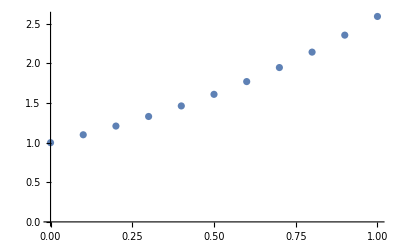

```mathematica
EulerStep[f_][{h_,t_,y_}]:={h,t+h,y+h f[t,y]}

f[t_,y_]:=y
h=0.1; t0=0.0; y0=1.0; EulerSteps=10;
EulerData=NestList[EulerStep[f],{h,t0,y0},EulerSteps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

Fixed step-size Euler does not fit our “Design Principles” because we have no idea if the answer is accurate and we have no idea if we picked a reasonable step size h.  What we really want is some way to automatically tune the step size to the solution of the ODE.  This is not as hard as it sounds!

## Euler’s Method (Alternate Derivation) and Taylor Methods

Another way to motivate Euler’s method is to look at the ODE
	y'(t)=f(t,y(t))
and say use the linear approximation
	y(t_k+h)≈y(t_k)+h y'(t_k)=y(t_k)+h f(t_k,y(t_k))
writing h_k for the size of step k, and t_k and y_k for the approximation generated this way we have
	t_(k+1) | = | t_k | + | h_k
y_(k+1) | = | y_k | + | h_k f(t_k,y_k)
h_(k+1) | = | ? |   |  
With some way of choosing the step sizes we would get an approximate solution values {y_k} at the points {t_k}.

The quadratic approximation
	y(t_k+h)≈y(t_k)+h y'(t_k)+h^2/2 y''(t_k)=y(t_k)+h f(t_k,y(t_k))+h^2/2?
should give a better answer if we can work out some way to compute (or approximate) y''(t_k).  The easiest thing to think about is to just differentiate the ODE
	y'(t)=f(t,y(t))
to get
	y''(t)=d/dt(f(t,y(t))=f_t(t,y(t))+f_y(t,y(t)).y'(t)=f_t(t,y(t))+f_y(t,y(t)).f(t,y(t))

The code is not that bad!

{{0.1,0.,1.},{0.1,0.1,1.105},{0.1,0.2,1.22103},{0.1,0.3,1.34923},{0.1,0.4,1.4909},{0.1,0.5,1.64745},{0.1,0.6,1.82043},{0.1,0.7,2.01157},{0.1,0.8,2.22279},{0.1,0.9,2.45618},{0.1,1.,2.71408}}

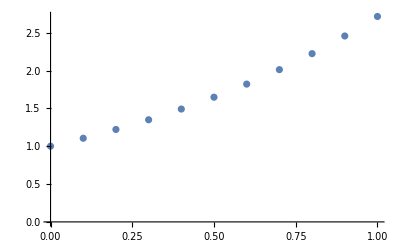

```mathematica
T2Step[f_,ft_,fy_][{h_,t_,y_}]:={h,t+h,y+h f[t,y]+h^2/2(ft[t,y]+fy[t,y]*f[t,y])}

f[t_,y_]:=y
ft[t_,y_]:=0
fy[t_,y_]:=1
h=0.1; t0=0.0; y0=1.0; T2Steps=10;
EulerData=NestList[T2Step[f,ft,fy],{h,t0,y0},T2Steps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

Of course, not everything has such clean derivatives as our simples example!

{{0.1,0.,1.},{0.1,0.1,1.05676},{0.1,0.2,1.12063},{0.1,0.3,1.1936},{0.1,0.4,1.27798},{0.1,0.5,1.37639},{0.1,0.6,1.49143},{0.1,0.7,1.6248},{0.1,0.8,1.77515},{0.1,0.9,1.93445},{0.1,1.,2.08447}}

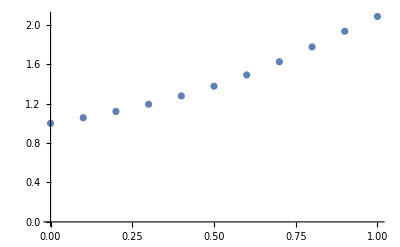

```mathematica
f[t_,y_]:=y Sin[t y]+ Cos[y]
ft[t_,y_]:=y^2 Cos[t y]
fy[t_,y_]:=t y Cos[t y]-Sin[y]+Sin[t y]
h=0.1; t0=0.0; y0=1.0; T2Steps=10;
EulerData=NestList[T2Step[f,ft,fy],{h,t0,y0},T2Steps]
ListPlot[ EulerData⟦All,2;;3⟧]
```

To generate the T3 scheme all we need to do is differentiate 
	y''(t)=f_t(t,y(t))+f_y(t,y(t)).f(t,y(t))	
again to get
	y'''=d/dt(f_t+f_y f)=f_tt+f_yt y'+(f_ty+f_yy)f+f_y d/dt(f)=f_tt+f_yt y'+(f_ty+f_yy)f+f_y(f_t+f_y y')=f_tt+f_yt f+(f_ty+f_yy)f+f_y(f_t+f_y f)
this looks like it is rapidly becoming unwieldy!  High order Taylor schemes are rarely used in practice because computing the required higher derivatives was problematic.

```mathematica
Clear[f,Eq,y,t]
Eq[1]=y'[t]->f[t,y[t]]
Eq[n_]:=Eq[n]=D[ Eq[n-1],t]
Simplify[Eq[2]/.Eq[1]]
Simplify[Eq[3]/.Eq[2]/.Eq[1]]
```

y'[t]→f[t,y[t]]

y''[t]→f[t,y[t]] f^(0,1)[t,y[t]]+f^(1,0)[t,y[t]]

y^(3)[t]→f[t,y[t]]^2 f^(0,2)[t,y[t]]+f^(0,1)[t,y[t]] f^(1,0)[t,y[t]]+f[t,y[t]] ((f^(0,1)[t,y[t]])^2+2 f^(1,1)[t,y[t]])+f^(2,0)[t,y[t]]

### Very Clean f: f(t,y)=y

It is clean if f is simple enough! For f(y)=y we have

```mathematica
Clear[f,Eq,y,t]
f[t_,y_]:=y
Eq[1]=y'[t]->f[t,y[t]]
Eq[n_]:=Eq[n]=D[ Eq[n-1],t]
Simplify[Eq[2]/.Eq[1]]
Simplify[Eq[3]/.Eq[2]/.Eq[1]]
```

y'[t]→y[t]

y''[t]→y[t]

y^(3)[t]→y[t]

It is clear that the Taylor Step Method is just building
	TS_k=y_0+t y_0+t^2/(2!)y_0+…+t^k/(k!)y_0=y_0(1+ t+t^2/2+…+t^k/(k!))≈y_0 e^t 
and we recognize the truncated Taylor polynomial for the exact solution.  This is not surprising when you look at how we built the Taylor Step.

In words, the TS method constructs and uses the degree k Taylor polynomial to advance the solution.

### Taylor Method Summary

The order k Taylor Step Method builds the truncated Taylor polynomial
	TS_k=y(t_0)+t y'(t_0)+t^2/(2!)y''(t_0)+…+t^k/(k!)y^(k)(t_0)
at the point y(t_0)by differentiating the ODE
	y'=f(t,y)
and repeatedly using the initial condition y(t_0)=y_0.  If it takes a step of size h then it makes an error
	(y^(k+1)(s))/(k+1)h^(k+1)
for some value of s satisfying  0≤s≤h.

This method is not used very often because it needs all those #$#@ derivatives!

We call any method with a single step error proportional to h^(k+1) a method of order k!  Can we find methods that do not need derivatives?

## RK Methods (overview)

We are going to restrict attention to autonomous ODEs
	y'=f(y) with  y(0)=y_0
to keep things tidy. If we are not allowed to differentiate the ODE we have to start with Euler. Suppose I take a half step with Euler
	y_(1/2)=y_0+0.5h f(y_0)
then I could take a second Euler step
	 y_1=y_(1/2)+0.5h f(y_(1/2))
and get one approximation y_1≈y(h).  Since I am willing to evaluate f twice I have other possibilities. For instance, I could do
	(ŷ)_1=y_0+h f(y_(1/2))≈y(h).
Is one better than the other?  Is some other possibility better than either? Would it be better to take more steps? Why go half way? …

Explicit RK methods are a family of simple ODE solvers based on this idea.  They are specified by a Butcher Tableau 
	c | A
  | b	
which tells you what internal steps to take and how to combine them.   The column vector c tells you where in time the internal steps are. The strictly lower triangular matrix A tells you how to compute the internal slopes. The row vector b tells you how to combine the internal slopes at the end. There is a partial list of RK methods on Wikipedia
	 https://en.wikipedia.org/wiki/List_of_Runge%E2%80%93Kutta_methods.

A Butcher Tableau 
	c | A
  | b_1
b_2	
with two row vectors b_1 and b_2 describes two different methods which use the same internal slopes.  The methods are compared to automatically adjust the step size h.  There is a partial list of embedded RK methods further down on the Wikipedia page
	 https://en.wikipedia.org/wiki/List_of_Runge%E2%80%93Kutta_methods#Embedded_methods.

## Simple RK Methods (Euler, MidPoint, Heun, Ralston, Generic)

The Butcher tables for these are

MidPoint:	0
1/2 | 0 | 0
1/2 | 0
  | 0 | 1

Heun:		0
1/2 | 0 | 0
1/2 | 0
  | 1/2 | 1/2

Ralston:	0
2/3 | 0 | 0
2/3 | 0
  | 1/4 | 3/4

Generic:	0
α | 0 | 0
α | 0
  | 1-1/(2α) | 1/(2 α)

Euler:		1 | 0
  | 1

For now we are not going to worry about how folks worked these out.  What we want to work out is how well the schemes match Taylor Series for the solution of 
	y'=f(y)
by differentiating the ODE.  I guess the first thing to do is implement these solvers

### Simple Implementations

```mathematica
HeunStep[f_][{h_,t_,y_}]:= Module[{K1,K2},
K1=f[y];
K2 = f[y+h/2 K1];
{h,t+h,y+h(1/2 K1 + 1/2 K2)}]

MidpointStep[f_][{h_,t_,y_}]:= Module[{K1,K2},
K1=f[y];
K2 = f[y+h/2 K1];
{h,t+h,y+h(0* K1 + K2)}]
```

The Taylor Series of the error tells us how good each of these schemes is. I am going to take this slowly with the MidPoint Method.

#### MidPoint Error Series

```mathematica
MidPtError[h_]=MidpointStep[f][{h,0,y0}]⟦3⟧-y[h]
```

y0+h f[y0+1/2 h f[y0]]-y[h]

The computer can compute a Taylor Series for us

```mathematica
TS=Series[MidPtError[h],{h,0, 3}]
```

(y0-y[0])+(f[y0]-y'[0]) h+1/2 (f[y0] f'[y0]-y''[0]) h^2+(1/8 f[y0]^2 f''[y0]-1/6 y^(3)[0]) h^3+O[h]^4

The first term is zero because of the initial condition. The second term is zero because of the ODE at the initial condition. The quadratic and cubic terms are less obvious.

Differentiating  the ODE and evaluating at t=0 gives
	y'[t]=f[y[t]]	⟹  	y''[t]=f_y[y[t]]y'[t]	⟹  	y''[0]=f_y[y_0]y'[t_0]=f_y[y_0]f[y_0]
The quadratic terms is zero!

Differentiating  the ODE again and evaluating at t=0 gives
	y'[t]=f[y[t]]	⟹  	y''[t]=f_y[y[t]]y'[t]	⟹  	y'''[t]=f_yy[y[t]]*y'[t]*y'[t]+f_y[y[t]]*y''[t]
Evaluating at t=0 gives
	y'''[0]=f_yy[y_0]*y'[0]*y'[0]+f_y[y_0]*y''[0]=f_yy[y_0]*f[y_0]*f[y_0]+f_y[y_0]*y''[0]=f_yy[y_0]*f[y_0]*f[y_0]+f_y[y_0]*f_y[y_0]*f[y_0]
It looks to me as though some (but not all) of the terms in the cubic match.  If we plug them in we get
	MidPtError[h]=0+0*h+0*h^2+ C(y_0)h^3+ O(h^4)
The midpoint scheme is second order because it matches the Taylor series up to second order with a non-zero third order error term.  We can automate this!

```mathematica
Clear[ODE,Subber,f,y,t]
ODE[0]=y'[t]->f[y[t]];
ODE[n_]:=Simplify[D[ODE[n-1],t]]//.Table[ODE[i],{i,0,n-2}]
Subber[n_]:= Join[{y[0]->y0},Table[ODE[i],{i,0,n}]/.{t->0,y[t]->y0}]
TableForm[Subber[3]]
```

y[0]→y0
y'[0]→f[y0]
y''[0]→f'[y0] y'[0]
y^(3)[0]→f[y0]^2 f''[y0]+f'[y0] y''[0]
y^(4)[0]→3 f[y0]^2 f'[y0] f''[y0]+f[y0]^3 f^(3)[y0]+f'[y0] y^(3)[0]

```mathematica
Simplify[Series[MidPtError[h],{h,0, 3}]//.Subber[3]]
```

-1/24 (f[y0] (4 f'[y0]^2+f[y0] f''[y0])) h^3+O[h]^4

#### Error and Order Discussion

If you had a second order scheme and a third order scheme which took the same amount of work. You would use the third order scheme. However,  in the real world third order schemes are more work than second order schemes!

There are fourth, fifth, sixth, … order schemes that were harder for folks to find and take more work per step than lower order schemes.

One common general purpose solver is the Dormand Prince RK pair
	https://en.wikipedia.org/wiki/Dormand%E2%80%93Prince_method
which contains an order 4 and order 5 solver using the same internal steps. The error is controlled by keeping the difference between the solvers small at each step.  This is the default solver in matlab ode45, simulink, and Octave.  It is the selected for moderate precision non-stiff problems by Mathematica’s heuristics.